Find Fixed Points

```mathematica
f=x^3-x;
g=-2y;
```

```mathematica
roots=Solve[{f==0,g==0},{x,y}]
```

{{x→-1,y→0},{x→0,y→0},{x→1,y→0}}

Define Jacobian Matrix

```mathematica
A[root_]:={{D[f,x]/.root,D[f,y]/.root},{D[g,x]/.root,D[g,y]/.root}};
```

Stability analysis for the origin

```mathematica
A[roots[[2]]]//MatrixForm
```

(-1 | 0
0 | -2)

```mathematica
Eigensystem[A[roots[[2]]]]
```

{{-2,-1},{{0,1},{1,0}}}

```mathematica
Eigensystem[A[roots[[1]]]] (* stability analysis of (-1,0) *)
```

{{-2,2},{{0,1},{1,0}}}

Stability Analysis of (1,0)

```mathematica
Eigensystem[A[roots[[3]]]]
```

{{-2,2},{{0,1},{1,0}}}

Now we generate the phase portrait

```mathematica
eqns={x'[t]==x[t]^3-x[t],y'[t]==-2y[t]};
ics1={x[0]==-1.0-0.1,y[0]==0};
ics2={x[0]==-1.0+0.01,y[0]==0};
ics3={x[0]==-1,y[0]==0.01};
ics4={x[0]==-1,y[0]==-0.01};
ics5={x[0]==1.0-0.01,y[0]==0};
ics6={x[0]==1.0+0.01,y[0]==0};
ics7={x[0]==1,y[0]==0.01};
ics8={x[0]==1,y[0]==-0.01};

ics9={x[0]==0.9,y[0]==2};
```

```mathematica
soln1=NDSolve[Append[eqns,ics1],{x,y},{t,0,1}];
soln2=NDSolve[Append[eqns,ics2],{x,y},{t,0,5}];
soln3=NDSolve[Append[eqns,ics3],{x,y},{t,0,-5}];
soln4=NDSolve[Append[eqns,ics4],{x,y},{t,0,-5}];
soln5=NDSolve[Append[eqns,ics5],{x,y},{t,0,5}];
soln6=NDSolve[Append[eqns,ics6],{x,y},{t,0,5}];
soln7=NDSolve[Append[eqns,ics7],{x,y},{t,0,-5}];
soln8=NDSolve[Append[eqns,ics8],{x,y},{t,0,-5}];

soln9=NDSolve[Append[eqns,ics9],{x,y},{t,0,5}];
```

NDSolve::ndsz: At t == 0.875633, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.96346, step size is effectively zero; singularity or stiff system suspected.

```mathematica
p1=ParametricPlot[Evaluate[{x[t],y[t]}/.soln1],{t,0,1}];
p2=ParametricPlot[Evaluate[{x[t],y[t]}/.soln2],{t,0,5}];
p3=ParametricPlot[Evaluate[{x[t],y[t]}/.soln3],{t,0,-5}];
p4=ParametricPlot[Evaluate[{x[t],y[t]}/.soln4],{t,0,-5}];
p5=ParametricPlot[Evaluate[{x[t],y[t]}/.soln5],{t,0,5}];
p6=ParametricPlot[Evaluate[{x[t],y[t]}/.soln6],{t,0,5}];
p7=ParametricPlot[Evaluate[{x[t],y[t]}/.soln7],{t,0,-5}];
p8=ParametricPlot[Evaluate[{x[t],y[t]}/.soln8],{t,0,-5}];

p9=ParametricPlot[Evaluate[{x[t],y[t]}/.soln9],{t,0,5}];
```

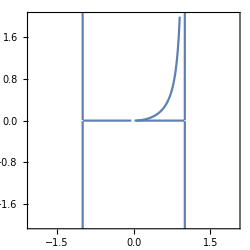

```mathematica
Show[p1,p2,p3,p4,p5,p6,p7,p8,p9,PlotRange->{{-2,2},{-2,2}},Frame->True,Axes-> False]
```

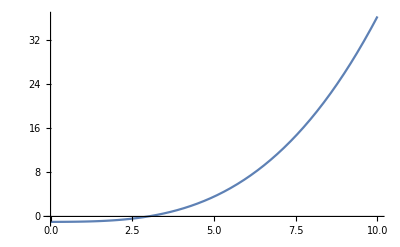

```mathematica
Plot[x[t]/.soln2,{t,0,10}]
```

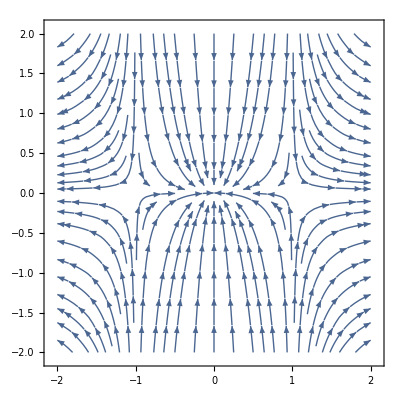

```mathematica
StreamPlot[{x^3-x,-2y},{x,-2,2},{y,-2,2}]
```